```mathematica
Abs[z]/(z*)-Sign[z]//FullSimplify
```

0

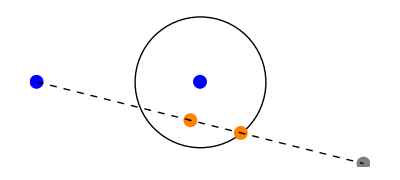

```mathematica
proj[z_,r_,c_]=(Re[z]c)/(z*);
intersect[z_,r_,c_]=ReIm[proj[z,r,c]+(√(r^2 Abs[z]^2-Im[z]^2 c^2))/(z*)];
x=1;R=.4;
Z=(2-.5ⅈ);
Show[
Graphics[{
Circle[{x,0},R],
PointSize[.025],
Blue,
Point[{{0,0},{x,0}}],
Gray,
Point[{ReIm[Z]}],
Orange,
Point[{ReIm[proj[Z,R,x]],intersect[Z,R,x]}],
Black,
Dashed,
Line[{{0,0},ReIm[Z]}]
}]
]
```